```mathematica
Clear[Evaluate[Context[]<>"*"]]
SetDirectory@NotebookDirectory[];
<<"../Definitions/Teukolsky.wl"
<<"../Definitions/SWSH.wl"
```

```mathematica
Graphics3D[Ellipsoid[{0,0,0},{√(2+2 √(1-a^2)),√(2+2 √(1-a^2)),1+ √(1-a^2)}/.a->0.9999999]]
```

-Graphics3D-

```mathematica
<<MaTeX`
TeX=MaTeX[#,
"Preamble"->{"\\usepackage{mathpazo}"},
FontSize->20]&;
```

```mathematica
θ0=45Degree;
radius=(1.1#)/First[#]&@{√(2+2 √(1-a^2)),√(2+2 √(1-a^2)),1+ √(1-a^2)}/.a->0.9;
text={Text[TeX@"\\Omega_H",FromSphericalCoordinates[{1.05,75°,-60°}]],
Text[TeX@"\\mathbf{\\hat{k}}",FromSphericalCoordinates[{2.2,θ0+12°,-30°}]]};
dist=2;
size=0.5;
vp={0.517162,-1.48664,0.722804};
rotθ0=RotationMatrix[θ0,{0,1,0}].RotationMatrix[45Degree,{0,0,1}];
bh=Ellipsoid[{0,0,0},radius];
bhline={First[ParametricPlot3D[1.05radius[[1]]{Cos[θ],Sin[θ],0},{θ,260°,340°},PlotStyle->Black]]/.Line[x_]:>{Arrowheads[0.02],Arrow[x]}};
vec={Thick,Arrow[{{0,0,-1.5},{0,0,1.5}}],Arrow[rotθ0.#&/@{{0,0,dist},0.7*{0,0,dist}}],Dashed,Line[{{0,0,0},rotθ0.{0,0,0.7*dist}}]};
wav={Opacity[0.5],Table[Polygon[rotθ0.(d*{0,0,dist}+size #)&/@{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}}],
{d,{1,1.05,1.1,1.15}}]};
Dynamic@vp
gr=Graphics3D[{bh,bhline,vec,wav,text},Boxed->False,ViewPoint->vp,ImageSize->Medium]
```

-Graphics3D-

```mathematica
Export["Figures/test.pdf",gr,RasterSize->400,ImageResolution->1000]
```

Figures/test.pdf

## Setup

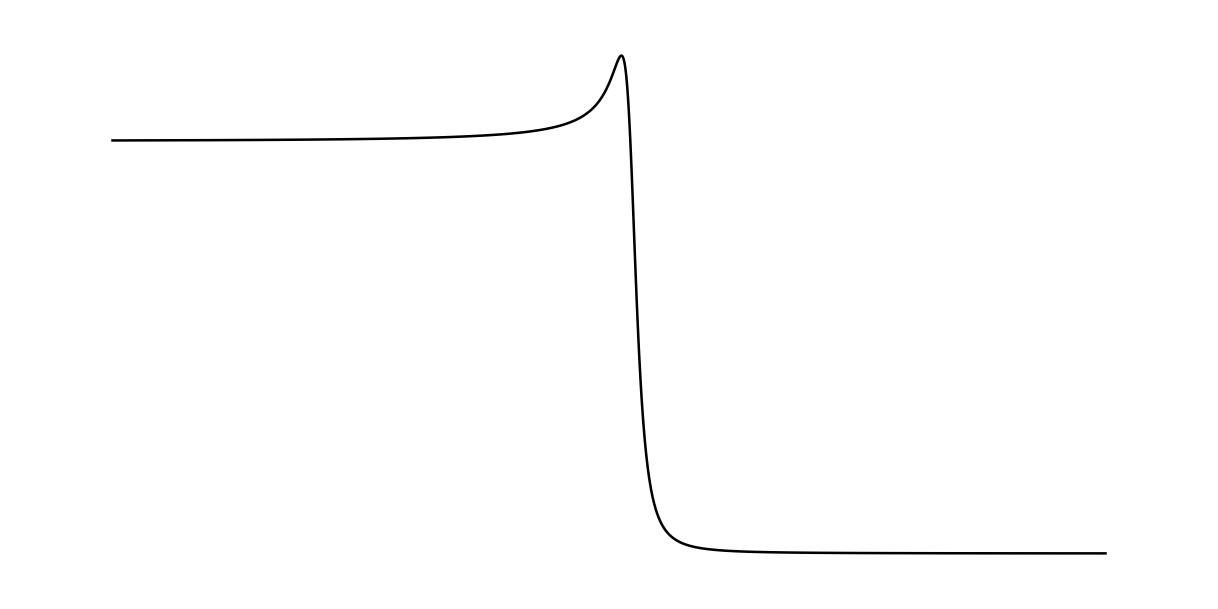

```mathematica
𝒢[r_]=s(r-M)/(r^2+a^2)+r Δ[r]/(r^2+a^2)^2;
Veff=(𝒦[r]^2-2 I s(r-M)𝒦[r]+Δ[r](4I r ω s-a^2 ω^2+2m a ω-ℰ+s(s+1)))/((r^2+a^2)^2)-𝒢[r]^2-Δ[r]/(r^2+a^2)𝒢'[r];

{rs,Vs}={Integrate[(r^2+a^2)/Δ[r],r],-Veff}//.{M->1,a->0.9999,ω->0.4,ℓ->1,m->1,s->1,ℰ->SpinWeightedSpheroidalHarmonicEigenvalue[s,ℓ,m,a ω]}//Chop;
pl2=ParametricPlot[{Re@rs,Re@Vs}//Evaluate,{r,1.001(1+Sqrt[1-0.9999^2]),220},PlotRange->All,AspectRatio->0.5,MaxRecursion->12,Axes->False,PlotStyle->Directive[Black,Thickness[0.0015]]]
```

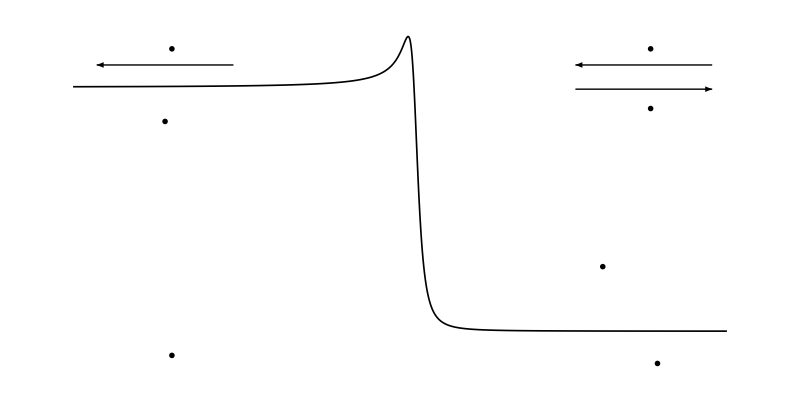

Figures/Veff.pdf

```mathematica
veff={
Text[TeX@"V_\\mathrm{eff} \\sim \\omega^2 + \\frac{2 i s \\omega}{r}",{180,-0.18}],
Text[TeX@"V_\\mathrm{eff} \\simeq \\left( \\kappa- i s \\frac{r_+ - M}{2 M r_+} \\right)^2 ~",{-175,-0.175}]};
Rsol={Text[TeX@"\\boxed{{}_{s}R_{\\ell m} \\simeq A_\\mathrm{hole} \\,\\Delta^{-s} \\,e^{- i \\kappa r_{*}}}",{-180,-0.03}],
Text[TeX@"\\boxed{{}_{s}R_{\\ell m}(r) \\sim A_\\mathrm{in}\\, \\frac{e^{-i \\omega r_*}}{r} + A_\\mathrm{out}\\, \\frac{e^{i \\omega r_*}}{r^{2s+1}}}",{140,-0.12}]};
currentJ={Text[TeX@"|A_\\mathrm{in}|^2",{175,0.015}],
Text[TeX@"|A_\\mathrm{out}|^2",{175,-0.022}],
Text[TeX@"|A_\\mathrm{hole}|^2",{-175,0.015}],
Thick,Arrowheads[0.025],Arrow@{{220,0.005},{120,0.005}},
Thick,Arrowheads[0.025],Arrow@{{120,-0.01},{220,-0.01}},
Thick,Arrowheads[0.025],Arrow@{{-130,0.005},{-230,0.005}}
};
Show[pl2,Graphics[{Rsol,veff,currentJ}],PlotRange->All,ImageSize->800]
Export["Figures/Veff.pdf",%]
```

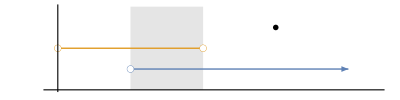

```mathematica
Show[
Graphics[{Text[TeX@"\\omega r_+ \\ll 1",{1.5,3}],Opacity[0.1],Rectangle[{0.5,0},{1,4}]}],
NumberLinePlot[{x>0.5,0<x<1},{x,0,2},PlotStyle->Thick],
PlotRange->{{-0.05,2.2},{0,4}},AspectRatio->0.25,Axes->{True,None},
Ticks->{{{0.5,TeX@"r_+",{0.02,0},Thick},{1,TeX@"~\\omega^{-1}",{0.02,0},Thick}},None},AxesOrigin->{0,0},
AxesLabel->{TeX@"r-r_{+}",None}
]
Export["validitySol.pdf",%];
```